```mathematica
Clear["Global`*"];
```

## Анализ результатов работы программы

```mathematica
datatrad1 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res2\\output_data_traditional_4096.txt", "Table"];datatrad2 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res2\\output_data_traditional_8192.txt", "Table"];
datablock1 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res2\\output_data_block_4096.txt", "Table"];
datablock2 = Import["C:\\WORK_DIRECTORY\\7_СЕМ\\ТПВ\\Лабораторные_работы\\PCT\\Lab_1\\res2\\output_data_block_8192.txt", "Table"];
```

```mathematica
data =Table[{datatrad1[[i]][[1]], datatrad1[[i]][[2]], datatrad2[[i]][[2]],datablock1[[i]][[2]], datablock2[[i]][[2]]}, {i, 1, Length@datablock1}];

data = Prepend[ data,{"Потоки","Традиционный алгоритм,  n = 4096","Традиционный алгоритм,  n = 8192","Блочный алгоритм, n = 4096","Блочный алгоритм, n = 8192"}];
Grid[data,Frame->All, Spacings->{1, 2}, ItemSize->{8, 2}]
```

Потоки | Традиционный алгоритм,  n = 4096 | Традиционный алгоритм,  n = 8192 | Блочный алгоритм, n = 4096 | Блочный алгоритм, n = 8192
1 | 23.5793 | 197.355 | 21.8061 | 174.864
2 | 12.6312 | 105.811 | 8.55241 | 71.1455
4 | 7.40453 | 64.8667 | 4.35046 | 36.5677
6 | 6.10845 | 55.5035 | 2.94796 | 24.6798
8 | 5.54501 | 51.0358 | 2.26398 | 18.6663
10 | 5.14723 | 48.2393 | 1.80005 | 15.0188
12 | 4.89782 | 46.9052 | 1.55197 | 12.8075
14 | 4.71355 | 46.387 | 1.38489 | 11.5329
16 | 4.62112 | 45.586 | 1.23774 | 10.3945
18 | 4.60683 | 45.271 | 1.15287 | 9.80296

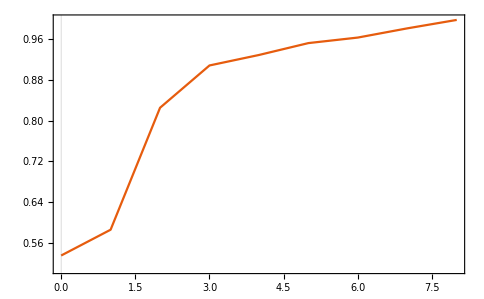

```mathematica
Show[ListLinePlot[Table[{i-2,(data[[i+1]][[2]])/(data[[i]][[2]])}, {i, 2, Length@data-1}], PlotTheme->"Scientific"]]
```

```mathematica
(data[[2]][[2]])/(data[[3]][[2]])
```

1.86675